```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
(****************************)
```

```mathematica
dateMouseListControl={{"113021","Mouse22428"},{"120221","Mouse22525"},{"121621","Mouse22525"},{"010622","Mouse22598"},{"011122","Mouse22598"},{"121121","Mouse22599"},{"121721","Mouse22599"},{"012122","Mouse22550"},{"011622","Mouse22550"},{"012322","Mouse22549"},{"012822","Mouse22549"},{"032923","Mouse23149"},{"033123","Mouse23149"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"120921","Mouse22485"},{"121821","Mouse22485"},{"011222","Mouse22501"},{"011822","Mouse22504"},{"012722","Mouse22504"},{"012322","Mouse22575"}};
```

```mathematica
(***LPaxons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"020922","Mouse22413"},{"021422","Mouse22413"},{"020122","Mouse22514"},{"012822","Mouse22514"},{"021122","Mouse22519"},{"021322","Mouse22519"},{"021122","Mouse22535"},{"021522","Mouse22535"},{"031522","Mouse22521"},{"031922","Mouse22521"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"022022","Mouse22563"},{"022222","Mouse22563"},{"031722","Mouse22539"},{"031722","Mouse22570"},{"032022","Mouse22539"},{"032022","Mouse22570"}};
```

```mathematica
(*****************************)
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(***Before-After paired loc mod indices***)
```

```mathematica
pairedLocModIndexSummaryValsControl=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","locModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}],1][[All,2]];
```

```mathematica
modIndicesLocControl=Table[(pairedLocModIndexSummaryValsControl[[n,2]]-pairedLocModIndexSummaryValsControl[[n,1]])/(pairedLocModIndexSummaryValsControl[[n,2]]+pairedLocModIndexSummaryValsControl[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsControl]}];
```

```mathematica
pairedLocModIndexSummaryValsV1axons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","locModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}],1][[All,2]];
```

```mathematica
modIndicesLocV1axons=Table[(pairedLocModIndexSummaryValsV1axons[[n,2]]-pairedLocModIndexSummaryValsV1axons[[n,1]])/(pairedLocModIndexSummaryValsV1axons[[n,2]]+pairedLocModIndexSummaryValsV1axons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsV1axons]}];
```

```mathematica
pairedLocModIndexSummaryValsLPaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","locModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}],1][[All,2]];
```

```mathematica
modIndicesLocLPaxons=Table[(pairedLocModIndexSummaryValsLPaxons[[n,2]]-pairedLocModIndexSummaryValsLPaxons[[n,1]])/(pairedLocModIndexSummaryValsLPaxons[[n,2]]+pairedLocModIndexSummaryValsLPaxons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsLPaxons]}];
```

```mathematica
pairedLocModIndexSummaryValsLMaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","locModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}],1][[All,2]];
```

```mathematica
modIndicesLocLMaxons=Table[(pairedLocModIndexSummaryValsLMaxons[[n,2]]-pairedLocModIndexSummaryValsLMaxons[[n,1]])/(pairedLocModIndexSummaryValsLMaxons[[n,2]]+pairedLocModIndexSummaryValsLMaxons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsLMaxons]}];
```

```mathematica
(*******************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S7D****************) 
(**********************************************)
```

```mathematica
controlLocModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedLocModIndexSummaryValsControl;
```

```mathematica
allLocModsControlDark=pairedLocModIndexSummaryValsControl[[All,1]];
```

```mathematica
allLocModsControlLED=pairedLocModIndexSummaryValsControl[[All,2]];
```

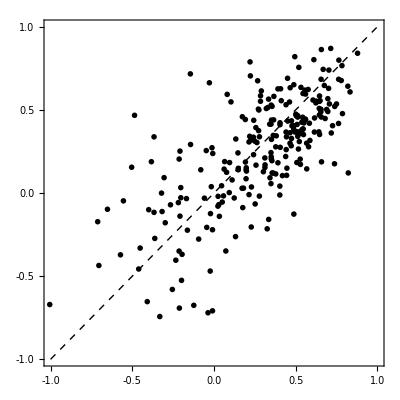

```mathematica
Show[ListPlot[pairedLocModIndexSummaryValsControl,PlotRange->{{-1,1},{-1,1}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{controlColor,PointSize[0.01]},FrameTicks->{{LinTizcks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-1,1},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
v1AxonsLocModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedLocModIndexSummaryValsV1axons;
```

```mathematica
allLocModsV1axonsDark=pairedLocModIndexSummaryValsV1axons[[All,1]];
```

```mathematica
allLocModsV1axonsLED=pairedLocModIndexSummaryValsV1axons[[All,2]];
```

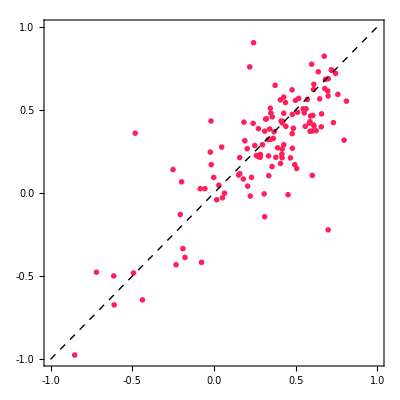

```mathematica
Show[ListPlot[pairedLocModIndexSummaryValsV1axons,PlotRange->{{-1,1},{-1,1}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{v1Color,PointSize[0.01]},FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-1,1},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
lpAxonsLocModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedLocModIndexSummaryValsLPaxons;
```

```mathematica
allLocModsLPaxonsDark=pairedLocModIndexSummaryValsLPaxons[[All,1]];
```

```mathematica
allLocModsLPaxonsLED=pairedLocModIndexSummaryValsLPaxons[[All,2]];
```

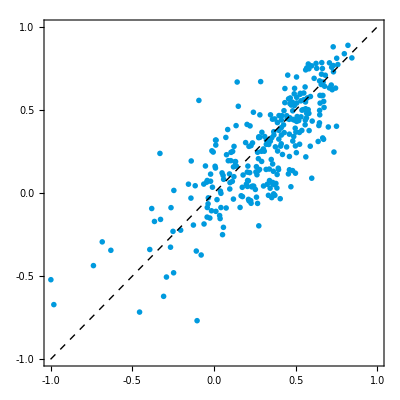

```mathematica
Show[ListPlot[pairedLocModIndexSummaryValsLPaxons,PlotRange->{{-1,1},{-1,1}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lpColor,PointSize[0.01]},FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-1,1},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
(*******************************************)
```

```mathematica
lmAxonsLocModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedLocModIndexSummaryValsLMaxons;
```

```mathematica
allLocModsLMaxonsDark=pairedLocModIndexSummaryValsLMaxons[[All,1]];
```

```mathematica
allLocModsLMaxonsLED=pairedLocModIndexSummaryValsLMaxons[[All,2]];
```

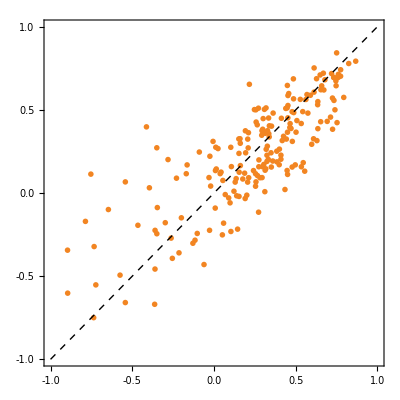

```mathematica
Show[ListPlot[pairedLocModIndexSummaryValsLMaxons,PlotRange->{{-1,1},{-1,1}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lmColor,PointSize[0.01]},FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-1,1},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
(****Histograms of differences between LED and Dark sessions*****)
```

```mathematica
controlLocModDiffs=Table[(pairedLocModIndexSummaryValsControl[[n,2]]-pairedLocModIndexSummaryValsControl[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsControl]}];
```

```mathematica
v1AxonsLocModDiffs=Table[(pairedLocModIndexSummaryValsV1axons[[n,2]]-pairedLocModIndexSummaryValsV1axons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsV1axons]}];
```

```mathematica
lpAxonsLocModDiffs=Table[(pairedLocModIndexSummaryValsLPaxons[[n,2]]-pairedLocModIndexSummaryValsLPaxons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsLPaxons]}];
```

```mathematica
lmAxonsLocModDiffs=Table[(pairedLocModIndexSummaryValsLMaxons[[n,2]]-pairedLocModIndexSummaryValsLMaxons[[n,1]]),{n,1,Length[pairedLocModIndexSummaryValsLMaxons]}];
```

```mathematica
(********)
```

```mathematica
bin=2*InterquartileRange[controlLocModDiffs]*(Length[controlLocModDiffs]^(-1/3));
```

```mathematica
minVal=-2;
```

```mathematica
maxVal=2;
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{controlLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Black}),PerformanceGoal->"Speed",PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
h2=Histogram[{controlLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->{{Black},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

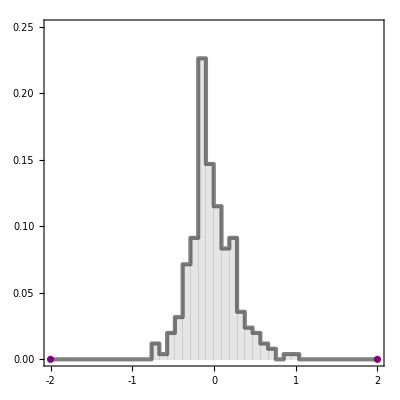

```mathematica
histLocModDiffsControl=Show[Show[hline,h2,ListPlot[{{-2,0},{2,0}},PlotStyle->Purple],PlotRange->{{minVal,maxVal},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minVal,maxVal,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(**)
```

```mathematica
bin=2*InterquartileRange[v1AxonsLocModDiffs]*(Length[v1AxonsLocModDiffs]^(-1/3))
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{v1AxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{v1Color}),PerformanceGoal->"Speed",PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
h2=Histogram[{v1AxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->{{v1Color},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

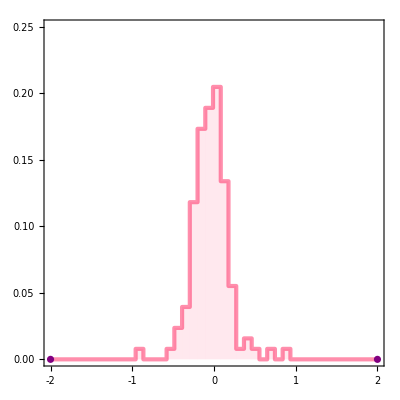

```mathematica
histLocModDiffsV1axons=Show[Show[hline,h2,ListPlot[{{-2,0},{2,0}},PlotStyle->Purple],PlotRange->{{minVal,maxVal},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minVal,maxVal,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(**)
```

```mathematica
bin=2*InterquartileRange[lpAxonsLocModDiffs]*(Length[lpAxonsLocModDiffs]^(-1/3));
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{lpAxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lpColor}),PerformanceGoal->"Speed",PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
h2=Histogram[{lpAxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->{{lpColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

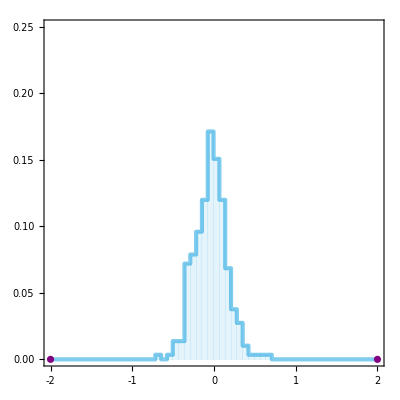

```mathematica
histLocModDiffsLPaxons=Show[Show[hline,h2,ListPlot[{{-2,0},{2,0}},PlotStyle->Purple],PlotRange->{{minVal,maxVal},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minVal,maxVal,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(**)
```

```mathematica
bin=2*InterquartileRange[lmAxonsLocModDiffs]*(Length[lmAxonsLocModDiffs]^(-1/3));
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{lmAxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lmColor}),PerformanceGoal->"Speed",PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
h2=Histogram[{lmAxonsLocModDiffs},{minVal,maxVal,bin},hfn,ChartStyle->{{lmColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{minVal,maxVal},{0,0.4}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

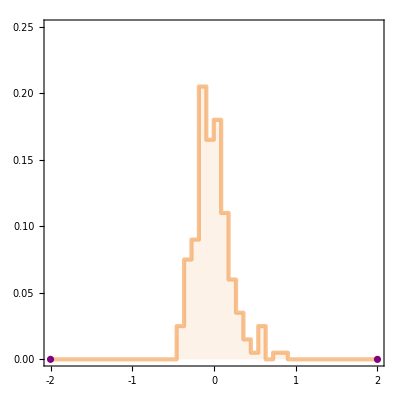

```mathematica
histLocModDiffsLMaxons=Show[Show[hline,h2,ListPlot[{{-2,0},{2,0}},PlotStyle->Purple],PlotRange->{{minVal,maxVal},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minVal,maxVal,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S7E****************) 
(**********************************************)
```

```mathematica
controlCharts=Show[BoxWhiskerChart[controlLocModDiffs,{{"Whiskers", Directive[Darker@controlColor,Thick]}, {"Fences", Directive[Darker@controlColor,Thick]},{"MedianMarker", Directive[Darker@controlColor,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[controlColor,Opacity[0.3]],Frame->False],DistributionChart[controlLocModDiffs,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],controlColor],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[v1AxonsLocModDiffs,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[v1AxonsLocModDiffs,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[lpAxonsLocModDiffs,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[lpAxonsLocModDiffs,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[lmAxonsLocModDiffs,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[lmAxonsLocModDiffs,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[controlLocModDiffs,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Transparent,Frame->False],DistributionChart[controlLocModDiffs,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

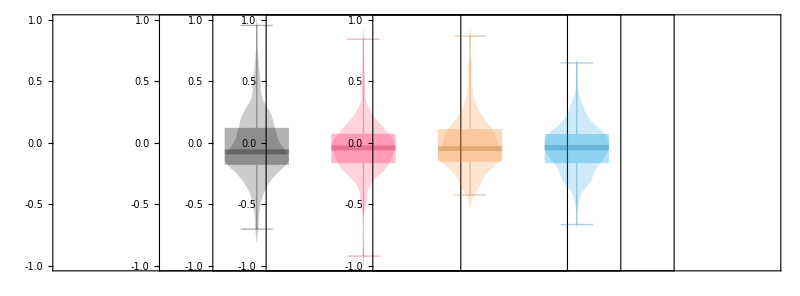

```mathematica
GraphicsRow[{controlCharts,v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```